```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{ke=1,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

```mathematica
(5600 60)/35000.000000
```

9.6

```mathematica
Sqrt[1.5 1.5+2 2]
```

2.5

```mathematica
1.5/2.5
```

0.6

```mathematica
270/0.8
```

337.5

```mathematica
270 3/2.
```

405.

```mathematica
270 1.5/2
```

202.5

```mathematica
337.5 0.6
```

202.5

```mathematica
337.5 0.8
```

270.

```mathematica
ComputeGrad[siga_,sigy_,pint_,pext_,de_,t_,young_,nu_,X1_,X2_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Block[{NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
gx= x1*ComputeColapseStrengthKT[NofD*x7,nYieldStrength*x2,PintofD*x8,nDe,nt*x3,nYoung,nNu,x4,x5,x6]-(PextofD*x9-PintofD*x8);
grad= {{D[gx,x1],D[gx,x2],D[gx,x3],D[gx,x4],D[gx,x5],D[gx,x6],D[gx,x7],D[gx,x8],D[gx,x9]}};
subst={NofD->siga,nYieldStrength->sigy,PintofD->pint,nDe->de,nt->t,nYoung->young,nNu->nu,PextofD->pext,x1->X1,x2->X2,x3->X3,x4->X4,x5->X5,x6->X6,x7->X7,x8->X8,x9->X9};
{{gx},grad}/.subst
];
```

```mathematica
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.0669397},{"YieldStress","NORMAL",87500.,2913.7500000000005},{"Thickness","NORMAL",0.9876,0.0019752000000000003},{"Ovality","WEIBULL MIN",0.66,0.132},{"Excent","WEIBULL MIN",13.2,2.64},{"Resid. Stress","NORMAL",-0.264,0.05280000000000001},{"Nax","DETERM",1.,0.},{"Pint","DETERM",1.,0.3},{"Pext","DETERM",1.,0.}}
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,87500.,2913.75},{Thickness,NORMAL,0.9876,0.0019752},{Ovality,WEIBULL MIN,0.66,0.132},{Excent,WEIBULL MIN,13.2,2.64},{Resid. Stress,NORMAL,-0.264,0.0528},{Nax,DETERM,1.,0.},{Pint,DETERM,1.,0.3},{Pext,DETERM,1.,0.}}

```mathematica
ComputeGrad[10000,80000,1000,2000,10,1,3 10^7,0.3,1,1,1,1,1,1,1,1,1]
```

{{19072.4},{{20072.4,19234.,21191.5,0.,0.,0.,-161.643,2000,-2000}}}

```mathematica
ComputeNumericalGradKT[{10000,80000,1000,2000,10,1,3 10^7,0.3},{1,1,1,1,1,1,1,1,1}]
```

{19072.4,{20072.4,19234.,21193.9,0.,0.,0.,-161.725,2000.,-2000.}}

```mathematica
ComputeColapseStrengthKT[10000,80000,1000,10,1,3 10^7,0.3,1,1,1]-(2000-1000)
```

19072.4

```mathematica
((ComputeColapseStrengthKT[10000+0.001,80000,1000,10,1.,3 10^7,0.3,1,1,1])-(ComputeColapseStrengthKT[10000.,80000,1000,10,1,3 10^7,0.3,1,1,1]))/0.001
```

-0.0161643

```mathematica
deriv=D[ComputeColapseStrengthKT[sigY,80000,1000,10,1,3 10^7,0.3,1,1,1],sigY];
```

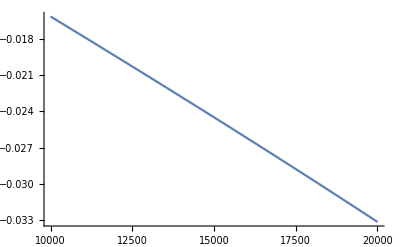

```mathematica
Plot[{deriv},{sigY,10000,20000}]
```

```mathematica
deriv/.sigY->10000.1
```

-0.0161645

```mathematica
x1*ComputeColapseStrengthKT[NofD*x7,nYieldStrength*x3,PintofD*x8,nDe,nt*x2,nYoung,nNu,x4,x5,x6]-(PextofD*x9-PintofD*x8);
```

```mathematica
ComputeNumericalGrad[NofD_,nYieldStrength_,PintofD_,PextofD_,nDe_,nt_,nYoung_,nNu_,X1_,X2_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Block[{dx=0.001,xvecn,xvecn1,dgdx,derivative,i},

Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[3]],PintofD*xvec[[8]],nDe,nt*xvec[[2]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn={X1,X2,X3,X4,X5,X6,X7,X8,X9};
derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{{Gx[xvecn]},{derivative}}
]
```

```mathematica
ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{vars,guess,dx=0.001,xvecn,xvecn1,dgdx,derivative,i,X1,X2,X3,X4,X5,X6,X7,X8,X9,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},
vars={NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu};
Gx[vars_,xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[vars[[1]]*xvec[[7]],vars[[2]]*xvec[[2]],vars[[3]]*xvec[[8]],vars[[5]],vars[[6]]*xvec[[3]],vars[[7]],vars[[8]],xvec[[4]],xvec[[5]],xvec[[6]]]-(vars[[4]]*xvec[[9]]-vars[[3]]*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];
For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[vars,xvecn1]-Gx[vars,xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[vars,xvecn],derivative}/.{NofD->Vars[[1]],nYieldStrength->Vars[[2]],PintofD->Vars[[3]],PextofD->Vars[[4]],nDe->Vars[[5]],nt->Vars[[6]],nYoung->Vars[[7]],nNu->Vars[[8]]}
]
```

```mathematica
ComputeNumericalGradKT[{50000,80000,10000,2000,10,1,3 10^7,0.3},{1,1,1,1,1,-1,1,1,1}]
ComputeGrad[50000,80000,10000,2000,10,1,3 10^7,0.3,1,1,1,1,1,-1,1,1,1]
ComputeNumericalGrad[50000,80000,10000,2000,10,1,3 10^7,0.3,1,1,1,1,1,-1,1,1,1]
```

{32288.,{24288.,20712.3,19380.5,-304.425,-9.34889,1054.91,-8102.26,20000.,-2000.}}

{{32288.},{{24288.,19379.8,20723.1,-304.439,-9.34891,1054.75,-8094.97,20000,-2000}}}

{{32288.},{{24288.,19380.5,20712.3,-304.425,-9.34889,1054.91,-8102.26,20000.,-2000.}}}

```mathematica
GRADX[fx]:=ComputeNumericalGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[2]];
GX[fx]:=ComputeNumericalGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[1]];
```

```mathematica
GRADX[{1,1,1,1,1,1,1,1,1}]
```

GRADX[{1,1,1,1,1,1,1,1,1}]

```mathematica
GX[{1,1,1,1,1,1,1,1,1}]
```

GX[{1,1,1,1,1,1,1,1,1}]

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
pBurstKS

];
```

```mathematica
ComputeGrad[n_,de_,t_,fu_,sa_,pi_,po_,X1_,X2_,X3_,X4_,X5_,X6_]:=Block[{NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
gx= x1*ComputeBurstResistance[n,x4*de,x2*t,x3*fu,sa,x5*po]-x6 pi;
grad= {{D[gx,x1],D[gx,x2],D[gx,x3],D[gx,x4],D[gx,x5],D[gx,x6]}};
subst={x1->X1,x2->X2,x3->X3,x4->X4,x5->X5,x6->X6};

{{gx},grad}/.subst
];
```

```mathematica
ComputeGrad[0.1,10,1,50000,10000,10000,2000,1,1,1,1,1,1]
```

{{2845.68},{{12845.7,12050.8,11060.3,-12050.8,2000,-10000}}}

```mathematica
ComputeNumericalGradKS[0.1,10,1,50000,10000,10000,2000,1,1,1,1,1,1]
```

ComputeNumericalGradKS[0.1,10,1,50000,10000,10000,2000,1,1,1,1,1,1]

```mathematica
ComputeNumericalGradKS[n_,de_,t_,fu_,sa_,pi_,po_,X1_,X2_,X3_,X4_,X5_,X6_]:=Block[{i,derivative,xvecn1,dgdx,dx=0.001,xvecn,NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},

Gx[xvec_]:= xvec[[1]]*ComputeBurstResistance[n,xvec[[4]]*de,xvec[[2]]*t,xvec[[3]]*fu,sa,xvec[[5]]*po]-xvec[[6]] pi;
xvecn={X1,X2,X3,X4,X5,X6};
derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{{Gx[xvecn]},{derivative}}
];
```

```mathematica
ComputeNumericalGrad[NofD_,nYieldStrength_,PintofD_,PextofD_,nDe_,nt_,nYoung_,nNu_,X1_,X2_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Block[{dx=0.001,xvecn,xvecn1,dgdx,derivative,i},

Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[3]],PintofD*xvec[[8]],nDe,nt*xvec[[2]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn={X1,X2,X3,X4,X5,X6,X7,X8,X9};
derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{{Gx[xvecn]},{derivative}}
]
```

```mathematica
ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{vars,guess,dx=0.001,xvecn,xvecn1,dgdx,derivative,i,X1,X2,X3,X4,X5,X6,X7,X8,X9,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},

{NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu}=Vars;
Gx[vars_,xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[2]],PintofD*xvec[[8]],nDe,nt*xvec[[3]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];
For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[vars,xvecn1]-Gx[vars,xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[vars,xvecn],derivative}(*/.{NofD->Vars[[1]],nYieldStrength->Vars[[2]],PintofD->Vars[[3]],PextofD->Vars[[4]],nDe->Vars[[5]],nt->Vars[[6]],nYoung->Vars[[7]],nNu->Vars[[8]]}*)
]
```